# ray tracing example: Kerr metric

This notebook will guide the user through the main features of the SimpleRayTracer package for Mathematica by use of the example of the Kerr metric. 

In principle, the full notebook can be generalized to arbitrary smooth (black-hole) spacetimes as long they are the metric is known in Boyer-Lindqvist (currently, only these are provided) coordinates. In the current version, also the Christoffel symbols have to be determined previously and have to be provided by the user (xAct integration may be implemented in the future).

The metric defines a spacetime in which the SimpleRayTracer package numerically determines lightlike geodesics.

## initialization

... load the package ...

```mathematica
<<SimpleRayTracer`;
```

========================================================================
SimpleRayTracer package is being loaded. =============================
=======================================================================

Set the Boyer-Lindquist coordinates (currently the automatic definition of the camera setup is not possible in other coordinates).

```mathematica
SetMass[M];
SetNewtonCoupling[G0];
SetSpin[α];
{$mass,$spin,$G0}
```

{M,α,G0}

```mathematica
SetBoyerLindquistCoords[t,r,θ,ϕ];
GetBoyerLindquistCoords[]
WhichCoords
```

{t,r,θ,ϕ}

BoyerLindquist

Specify metric and connection (Christoffel symbols). Inverse metric is determined by the package itself.

```mathematica
SetMetric[gMetric, {
	{-1+(2 M r)/(r^2+α^2 Cos[θ]^2),0,0,-(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)},
	{0,(r^2+α^2 Cos[θ]^2)/(-2 M r+r^2+α^2),0,0},
	{0,0,r^2+α^2 Cos[θ]^2,0},
	{-(2 M r α Sin[θ]^2)/(r^2+α^2 Cos[θ]^2),0,0,((2 M r (r^2+α^2)+(-2 M r+r^2+α^2) (r^2+α^2 Cos[θ]^2)) Sin[θ]^2)/(r^2+α^2 Cos[θ]^2)}
}]
```

```mathematica
SetChristoffel[christoffelOf[gMetric],{
	{
		{0,-(2 M (r^2+α^2) (-2 r^2+α^2+α^2 Cos[2 θ]))/((-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),-(4 M r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},
		{-(2 M (r^2+α^2) (-2 r^2+α^2+α^2 Cos[2 θ]))/((-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(2 M α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},
		{-(4 M r α^2 Sin[2 θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,(8 M r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2)},
		{0,(2 M α (-6 r^4-3 r^2 α^2+α^4+(-r^2 α^2+α^4) Cos[2 θ]) Sin[θ]^2)/((-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),(8 M r α^3 Cos[θ] Sin[θ]^3)/((2 r^2+α^2+α^2 Cos[2 θ])^2),0}
	},
	{
		{(M (-2 M r+r^2+α^2) (r^2-α^2 Cos[θ]^2))/((r^2+α^2 Cos[θ]^2)^3),0,0,(M α (-2 M r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/((r^2+α^2 Cos[θ]^2)^3)},
		{0,(r (-M r+α^2)+(M-r) α^2 Cos[θ]^2)/((-2 M r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},
		{0,-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),-(r (-2 M r+r^2+α^2))/(r^2+α^2 Cos[θ]^2),0},
		{(M α (-2 M r+r^2+α^2) (-r^2+α^2 Cos[θ]^2) Sin[θ]^2)/((r^2+α^2 Cos[θ]^2)^3),0,0,-((-2 M r+r^2+α^2) (r^5-M r^2 α^2+α^2 (2 r^3+M (r^2+α^2)) Cos[θ]^2-(M-r) α^4 Cos[θ]^4) Sin[θ]^2)/((r^2+α^2 Cos[θ]^2)^3)}
	},
	{
		{-(2 M r α^2 Cos[θ] Sin[θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,(M r α (r^2+α^2) Sin[2 θ])/((r^2+α^2 Cos[θ]^2)^3)},
		{0,(α^2 Cos[θ] Sin[θ])/((-2 M r+r^2+α^2) (r^2+α^2 Cos[θ]^2)),r/(r^2+α^2 Cos[θ]^2),0},
		{0,r/(r^2+α^2 Cos[θ]^2),-(α^2 Cos[θ] Sin[θ])/(r^2+α^2 Cos[θ]^2),0},
		{(M r α (r^2+α^2) Sin[2 θ])/((r^2+α^2 Cos[θ]^2)^3),0,0,-((8 r^6+16 M r^3 α^2+16 r^4 α^2+10 M r α^4+11 r^2 α^4+3 α^6+4 α^2 (-2 M r+r^2+α^2) (2 r^2+α^2) Cos[2 θ]+α^4 (-2 M r+r^2+α^2) Cos[4 θ]) Sin[2 θ])/(16 (r^2+α^2 Cos[θ]^2)^3)}
	},
	{
		{0,(M α (r^2-α^2 Cos[θ]^2))/((-2 M r+r^2+α^2) (r^2+α^2 Cos[θ]^2)^2),-(8 M r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0},
		{(M α (r^2-α^2 Cos[θ]^2))/((-2 M r+r^2+α^2) (r^2+α^2 Cos[θ]^2)^2),0,0,(-16 M r^4+8 r^5-12 M r^2 α^2+8 r^3 α^2+M α^4+3 r α^4+4 r α^2 (-M r+2 r^2+α^2) Cos[2 θ]-(M-r) α^4 Cos[4 θ])/(2 (-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)},
		{-(8 M r α Cot[θ])/((2 r^2+α^2+α^2 Cos[2 θ])^2),0,0,((8 r^4+8 M r α^2+8 r^2 α^2+3 α^4+4 α^2 (2 r (-M+r)+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2)},
		{0,(-16 M r^4+8 r^5-12 M r^2 α^2+8 r^3 α^2+M α^4+3 r α^4+4 r α^2 (-M r+2 r^2+α^2) Cos[2 θ]-(M-r) α^4 Cos[4 θ])/(2 (-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2),((8 r^4+8 M r α^2+8 r^2 α^2+3 α^4+4 α^2 (2 r (-M+r)+α^2) Cos[2 θ]+α^4 Cos[4 θ]) Cot[θ])/(2 (2 r^2+α^2+α^2 Cos[2 θ])^2),0}
	}
}];
```

After metric and/or Christoffels have been set, these can be output to check successful initialization.

```mathematica
GetMetric[1,1]//Simplify
```

-(4 (r^2+α^2 Cos[θ]^2) (r (r^3+2 M α^2+r α^2)+α^2 (-2 M r+r^2+α^2) Cos[θ]^2))/((-2 M r+r^2+α^2) (2 r^2+α^2+α^2 Cos[2 θ])^2)

```mathematica
GetChristoffel[2,-1,-1]//Simplify
```

(M (-2 M r+r^2+α^2) (r^2-α^2 Cos[θ]^2))/((r^2+α^2 Cos[θ]^2)^3)

## single ray traces

The Kerr metric which was initialized before has two free parameters: the mass M, and the spin parameter α.  In general, all such parameter values have to be passed as rules to all the numerical functions.

GetSingleLightRay[rCam_,θCam_,ϕCam_},{xScreen_,yScreen_},paramRules_List] 
is a function which to numerically integrate the geodesic equation of a single light ray in the presently set spacetime.
PlotSingleTrajectory[sol_, paramRules_List]
is a plot routine to plot the outcome of GetSingleLightRay[]. It takes the same options as Mathematica’s Plot3D routine. In addition the user can specify to plot the horizon or not.

```mathematica
?GetSingleLightRay
?PlotSingleTrajectory
```

You can explore single light rays by varying the screen coordinates below

```mathematica
screenX = Rationalize[0,1*^-100];
screenY = Rationalize[4.916,1*^-100];
params = {M->1,α->9/10};

sol = GetSingleLightRay[{100,π,0},{screenX,screenY},params,WorkingPrecision->20][[1]];
Quiet@PlotSingleTrajectory[sol, params, PlotRange->{{-10,10},{-10,10},{-10,10}}]
```

trajectory escapes: at λ=230.50 the radial coordinate has surpassed the radial camera distance

{-10,10}

-Graphics3D-

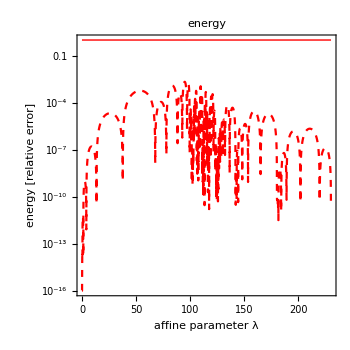

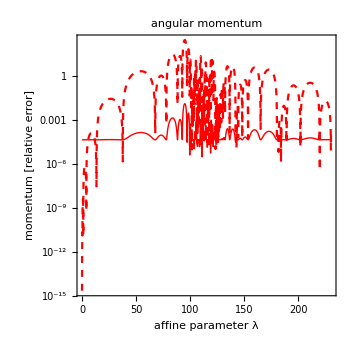

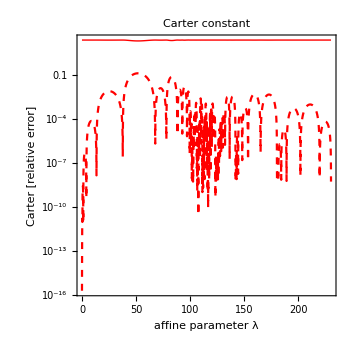

maximalErrors | 0.00218709 | 291.088 | 0.127879
finalTimeErrors | 6.8063921×10^-11 | 0.000083163339662 | 5.4527646×10^-9

```mathematica
CheckConstantsOfMotionAlongRay[sol,{M->1,α->9/10},α]//TableForm
```

## shadow boundary

BoundaryBisection[{rCam_,θCam_,ϕCam_}, {{xInnerScreen_,yInnerScreen_}, {xOuterScreen_,yOuterScreen_}}, paramRules_, precisionAim_]
is a routine to perform bisections in a user-defined interval to determine the location of the shadow boundary (if present) within this interval.

```mathematica
?BoundaryBisection
```

BoundaryBisection[{rCam_,θCam_,ϕCam_}, {{xInnerScreen_,yInnerScreen_}, {xOuterScreen_,yOuterScreen_}}, paramRules_, precisionAim_]

### sub-extremal example

You can obtain a single bisection between two screen points to see whether there is a shadow boundary between those points.

```mathematica
x1 = 0; y1 = 0;
x2 = 5; y2 = 5;

Quiet@BoundaryBisection[{100,π/2,0},{{x1,y1},{x2,y2}},{M->1,α->9/10},1/1000]
```

shadow boundary was found within the specified interval.

{2.40387,2.40387}

Once you have a good idea where the shadow is roughly located, you can obtain a parametric curve of the shadow boundary.

```mathematica
?GetParametricShadowBoundary
```

GetParametricShadowBoundary[{rCam_,θCam_,ϕCam_}, {xCenter_,yCenter_}, radialSweepDistance_, {ψmin_,ψmax_,ψstepSize_}, paramRules_, precisionAim_]

```mathematica
sol = Quiet@GetParametricShadowBoundary[{100,π/2,0}, {0,0}, 8, {1/1000,π,π/100}, {M->1,α->9/10}, 1/1000];
```

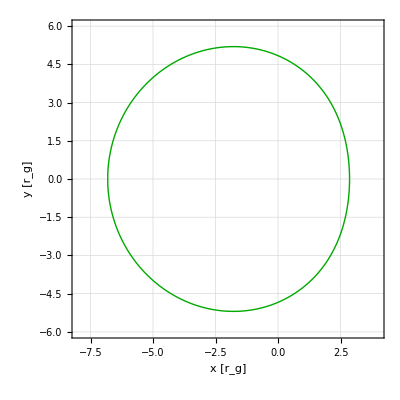

```mathematica
ListPlot[
	Join[sol[[All,2]], Reverse[{#[[1]],-#[[2]]}&/@sol[[All,2]]]],
	PlotRange->{{-8,4},{-6,6}},Joined->True, Axes->False, 
	GridLines->Automatic, GridLinesStyle->Directive[Thin,Lighter@Lighter@Lighter@Gray],
	PlotStyle->{{Darker@Green, Thick}},
	Frame->True, FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},
	FrameLabel->{"x [r_g]", "y [r_g]"}, LabelStyle->{Black,16,FontFamily->"Helvetica"},
	ImageSize->400, AspectRatio->1
]
```

### extremal example

You can obtain a single bisection between two screen points to see whether there is a shadow boundary between those points.

```mathematica
x1 = 0; y1 = 0;
x2 = 1/100; y2 = 5;
```

```mathematica
BoundaryBisection[{100,π/2,0},{{x1,y1},{x2,y2}},{M->1,α->999/1000},1/100]
```

NDSolve::ndsz: At λ == 99.793788061621508664, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 101.40612374987632377, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 103.64653491529255207, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

shadow boundary was found within the specified interval.

{0.00946289,4.73145}

```mathematica
BoundaryBisection[{100,π/2,0},{{x1,y1},{x2,y2}},{M->1,α->99999/100000},1/100]
```

NDSolve::ndsz: At λ == 99.827112394489668443, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 101.43585307446659759, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 103.68477338496815474, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

shadow boundary was found within the specified interval.

{0.00946289,4.73145}

```mathematica
BoundaryBisection[{100,π/2,0},{{x1,y1},{x2,y2}},{M->1,α->1},1/100]
```

NDSolve::ndsz: At λ == 99.830678928674013336, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 101.43902285036958715, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 103.68820331606915924, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

shadow boundary was found within the specified interval.

{0.00946289,4.73145}

```mathematica
BoundaryBisection[{100,π/2,0},{{x1,y1},{x2,y2}},{M->1,α->1+1*^-5},1/100]
```

probably no shadow boundary between the two specified points.

None

## check deflection angle error with radial distance (check whether drift to different value comes from definition of Boyer-Lindquist coordinates)

```mathematica
deflectionAngleTable = {};

radialDistanceTable = Table[Exp[x],{x,4,13,1/5}];
%//N
```

{54.5982,66.6863,81.4509,99.4843,121.51,148.413,181.272,221.406,270.426,330.3,403.429,492.749,601.845,735.095,897.847,1096.63,1339.43,1635.98,1998.2,2440.6,2980.96,3640.95,4447.07,5431.66,6634.24,8103.08,9897.13,12088.4,14764.8,18033.7,22026.5,26903.2,32859.6,40134.8,49020.8,59874.1,73130.4,89321.7,109098.,133252.,162755.,198789.,242802.,296559.,362217.,442413.}

```mathematica
Timing[Do[
	radialCameraDistance = radialDistanceTable[[ii]];
	
	sol = Check[
		GetSingleLightRay[{radialCameraDistance,π/2,0},{10,0},{M->1,α->0.9}][[1]],
		None
	];
	
	Print@(((x[4][λ]/.sol/.λ->Head[sol[[3,2]]][[1,1,2]])-π)/π);
	AppendTo[deflectionAngleTable,{radialDistanceTable[[ii]],((x[4][λ]/.sol/.λ->Head[sol[[3,2]]][[1,1,2]])-π)/π}];
,
	{ii,Length@radialDistanceTable}
]]
```

trajectory escapes: at λ=111.56086013828425818 the radial coordinate has surpassed the radial camera distance

0.103664593747129253

trajectory escapes: at λ=135.86391193382461665 the radial coordinate has surpassed the radial camera distance

0.113960134366387259

trajectory escapes: at λ=165.50059190686757157 the radial coordinate has surpassed the radial camera distance

0.122380590106218112

trajectory escapes: at λ=201.65854553551704887 the radial coordinate has surpassed the radial camera distance

0.129277401946212681

trajectory escapes: at λ=245.78746772140913553 the radial coordinate has surpassed the radial camera distance

0.1349305530917631477

trajectory escapes: at λ=299.65730439460781992 the radial coordinate has surpassed the radial camera distance

0.1395658712672839548

trajectory escapes: at λ=365.42923639974974123 the radial coordinate has surpassed the radial camera distance

0.1433669545009654146

trajectory escapes: at λ=445.74235120630952045 the radial coordinate has surpassed the radial camera distance

0.1464837866340029559

trajectory escapes: at λ=543.81949698308054636 the radial coordinate has surpassed the radial camera distance

0.1490392309491063669

trajectory escapes: at λ=663.59657786900245407 the radial coordinate has surpassed the radial camera distance

0.1511340832161087815

trajectory escapes: at λ=809.88047818989147396 the radial coordinate has surpassed the radial camera distance

0.1528510841582074667

trajectory escapes: at λ=988.54195700573218009 the radial coordinate has surpassed the radial camera distance

0.1542581713574396294

trajectory escapes: at λ=1206.7512389501124634 the radial coordinate has surpassed the radial camera distance

0.1554111229404508711

trajectory escapes: at λ=1473.2657692882432207 the radial coordinate has surpassed the radial camera distance

0.1563557169290538

trajectory escapes: at λ=1798.7816712038483511 the radial coordinate has surpassed the radial camera distance

0.1571295235091311233

trajectory escapes: at λ=2196.3630175170357666 the radial coordinate has surpassed the radial camera distance

0.1577633668737377059

trajectory escapes: at λ=2681.9661177143172590 the radial coordinate has surpassed the radial camera distance

0.1582825134078866027

trajectory escapes: at λ=3275.0799246401256945 the radial coordinate has surpassed the radial camera distance

0.1587076965446903116

trajectory escapes: at λ=3999.5081681082358313 the radial coordinate has surpassed the radial camera distance

0.1590558937584546273

trajectory escapes: at λ=4884.3246872908981800 the radial coordinate has surpassed the radial camera distance

0.1593410418278087088

trajectory escapes: at λ=5965.0402743628176433 the radial coordinate has surpassed the radial camera distance

0.1595745448474454558

trajectory escapes: at λ=7285.0278443423946534 the radial coordinate has surpassed the radial camera distance

0.1597657499167383768

trajectory escapes: at λ=8897.2631247368693717 the radial coordinate has surpassed the radial camera distance

0.159922316178006545

trajectory escapes: at λ=10866.450773918118583 the radial coordinate has surpassed the radial camera distance

0.1600505398651555331

trajectory escapes: at λ=13271.621213428590381 the radial coordinate has surpassed the radial camera distance

0.1601554770184333626

trajectory escapes: at λ=16209.302376751134193 the radial coordinate has surpassed the radial camera distance

0.1602414249920372687

trajectory escapes: at λ=19797.393717025262888 the radial coordinate has surpassed the radial camera distance

0.1603118053243370556

trajectory escapes: at λ=24179.897940781497131 the radial coordinate has surpassed the radial camera distance

0.1603694379201042632

trajectory escapes: at λ=29532.700341362538005 the radial coordinate has surpassed the radial camera distance

0.1604166213612558057

trajectory escapes: at λ=36070.627659724674435 the radial coordinate has surpassed the radial camera distance

0.1604552501346176618

trajectory escapes: at λ=44056.069879598518434 the radial coordinate has surpassed the radial camera distance

0.1604869546958878823

trajectory escapes: at λ=53809.510857274369275 the radial coordinate has surpassed the radial camera distance

0.1605127869079781287

trajectory escapes: at λ=65722.390371310197985 the radial coordinate has surpassed the radial camera distance

0.1605339830175774138

trajectory escapes: at λ=80272.814149895330143 the radial coordinate has surpassed the radial camera distance

0.1605513501522905131

trajectory escapes: at λ=98044.741778178242544 the radial coordinate has surpassed the radial camera distance

0.160565641900607772

trajectory escapes: at λ=119751.42313032026821 the radial coordinate has surpassed the radial camera distance

0.1605772555455922023

trajectory escapes: at λ=146264.02352167952811 the radial coordinate has surpassed the radial camera distance

0.1605867555231761312

trajectory escapes: at λ=178646.58666296637711 the radial coordinate has surpassed the radial camera distance

0.1605945111349824603

trajectory escapes: at λ=218198.73865232316094 the radial coordinate has surpassed the radial camera distance

0.1606011454512195262

trajectory escapes: at λ=266507.84627934488477 the radial coordinate has surpassed the radial camera distance

0.160606438277893297

trajectory escapes: at λ=325512.72308011022632 the radial coordinate has surpassed the radial camera distance

0.1606106186874742688

trajectory escapes: at λ=397581.44246844863286 the radial coordinate has surpassed the radial camera distance

0.1606141636917000115

trajectory escapes: at λ=485606.37542596830798 the radial coordinate has surpassed the radial camera distance

0.1606171185127329954

trajectory escapes: at λ=593120.27143660470252 the radial coordinate has surpassed the radial camera distance

0.160620411640324189

trajectory escapes: at λ=724438.03969346654218 the radial coordinate has surpassed the radial camera distance

0.1606218889758197855

trajectory escapes: at λ=884829.92451867293822 the radial coordinate has surpassed the radial camera distance

0.1606229721658611024

{39.096,Null}

```mathematica
deflectionAngleTable
```

{{ⅇ^4,3.9877577965837318},{ⅇ^(21/5),4.4180186033898391},{ⅇ^(22/5),5.127641373120008},{ⅇ^(23/5),6.563874832663451238},{ⅇ^(24/5),4.911996578334272614},{ⅇ^5,4.473834084231935935},{ⅇ^(26/5),4.235543110063486667},{ⅇ^(27/5),4.082250968023320559},{ⅇ^(28/5),3.975477602485049335},{ⅇ^(29/5),3.897597879320477042},{ⅇ^6,3.839070748229268996},{ⅇ^(31/5),3.794175841394046068},{ⅇ^(32/5),3.759232617140928477},{ⅇ^(33/5),3.731737572767364335},{ⅇ^(34/5),3.709925132294849611},{ⅇ^7,3.69249263628156311},{ⅇ^(36/5),3.678511570886213677},{ⅇ^(37/5),3.667245582980966565},{ⅇ^(38/5),3.658142334966177885},{ⅇ^(39/5),3.650778884600912665},{ⅇ^8,3.644779174986806123},{ⅇ^(41/5),3.639913098816274936},{ⅇ^(42/5),3.635971013667612253},{ⅇ^(43/5),3.632736978290827331},{ⅇ^(44/5),3.630087397875575652},{ⅇ^9,3.627974101553599572},{ⅇ^(46/5),3.6262691665394895},{ⅇ^(47/5),3.624753786766495912},{ⅇ^(48/5),3.623636465649961704},{ⅇ^(49/5),3.622635740659757746},{ⅇ^10,3.621885615302422524},{ⅇ^(51/5),3.621305037517085071},{ⅇ^(52/5),3.62073628714216372},{ⅇ^(53/5),3.6203413783172073},{ⅇ^(54/5),3.620211822478647023},{ⅇ^11,3.619782825632511589},{ⅇ^(56/5),3.619649228529215346},{ⅇ^(57/5),3.619434880935322444},{ⅇ^(58/5),3.619906097051063339},{ⅇ^(59/5),3.619491525174172451},{ⅇ^12,3.619464084889314974},{ⅇ^(61/5),3.620290761946114254},{ⅇ^(62/5),3.619812493650269464},{ⅇ^(63/5),3.620822458567370934},{ⅇ^(64/5),3.61951416682139512},{ⅇ^13,3.620653214836232303}}

{a→0.160612699456586011,k→3.11427294108482884}

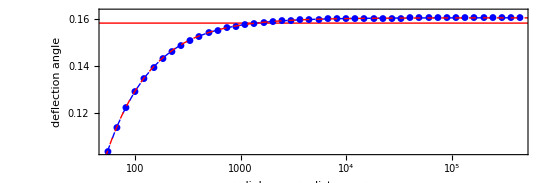

```mathematica
data = deflectionAngleTable;
iyerHansen = 0.15838356007923815;

(*model=Log[Exp[a]-k/t];*)
model=a-k/t;
fit=FindFit[data,model,{a,k},t]

Show[
	ListLogLinearPlot[deflectionAngleTable, PlotStyle->{{Thick,Blue,Dashed}},
		Joined->True, PlotMarkers->Automatic,
		Frame->True, FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},
		FrameLabel->{"radial camera distance r_cam","deflection angle"}, LabelStyle->{Black,16,FontFamily->"Helvetica"},
		ImageSize->550, AspectRatio->1/3, PlotRange->{deflectionAngleTable[[1,2]],deflectionAngleTable[[-1,2]]+0.0025}
	],
	LogLinearPlot[iyerHansen,{x,1*^-10,1*^10}, PlotStyle->{Thick,Red}],
	LogLinearPlot[model/.fit,{t,1*^-10,1*^10}, PlotStyle->{Thick,Red,Dashed}]
]
```

## shadow image (accretion-disk model) (*preliminary testing*)

### test

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{0,0,10/3,1}];
GetIntensity[{300,π/3,0},{9,9},{M->1,α->-9/10},ode,WorkingPrecision->30,PrecisionGoal->4]
```

trajectory escapes: at λ=632.57 the radial coordinate has surpassed the radial camera distance

16.88

```mathematica
screenBoundary = 10;
pixels = 1000;
screenPoints = Flatten[Table[{screenXVal,screenYVal},{screenXVal,-screenBoundary+1/100,screenBoundary+2/100,(2screenBoundary)/(Sqrt@pixels)},{screenYVal,-screenBoundary+1/100,screenBoundary+2/100,(2screenBoundary)/(Sqrt@pixels)}],1];
intensityList = GetIntensityData[{300,π/3,0},{M->1,α->-9/10},screenPoints,WorkingPrecision->30,PrecisionGoal->4];

RandomSample[intensityList][[1;;2]]//N//TableForm
```

Numerical integration of the radiative transfer equation did not converge for1/1024 screen points. Try to incrase WorkinPrecision and test single points to see error messages.

-1.13562 | 9.61612 | 11.033
-6.82772 | -9.99 | 8.80846

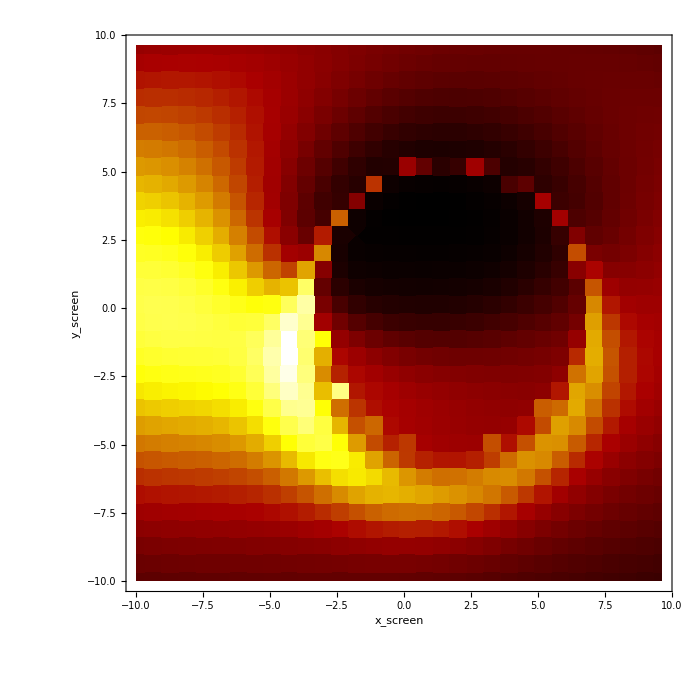

```mathematica
plotData = Cases[intensityList,{x_,y_,i_?NumericQ}];

ListDensityPlot[
	Evaluate[Table[{plotData[[i,1]],plotData[[i,2]],plotData[[i,3]]},{i,Length@plotData}]],
	ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],ClippingStyle->{Black,White},
	Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
	FrameLabel->{"x_screen","y_screen"}, LabelStyle->{32,Black},
	InterpolationOrder->0, Background->None, ImageSize->700
]
```

### code comparison to EXACT_GRRT MODEL-1

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{0,-3,0,0}];
```

#### load comparison data

This loads the image data from TESTCASE 1 and plots it

```mathematica
SetDirectory[NotebookDirectory[]];
intensityEXACT=
Quiet[ToExpression/@Import["EXACT_GRRT_TEST_1_FULL.dat"]];
```

```mathematica
plotDataEXACT = Cases[intensityEXACT[[All,1;;3]],{b_,c_,a_}/;10^2>a>10^-10];
```

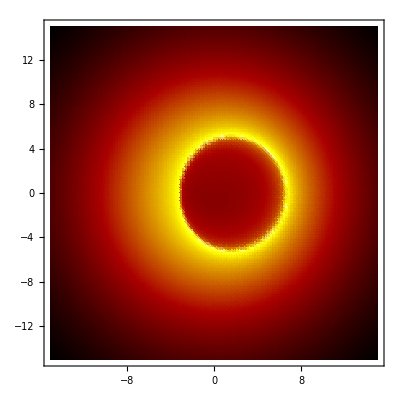

```mathematica
Table[{plotDataEXACT[[i,1]],plotDataEXACT[[i,2]],plotDataEXACT[[i,3]]/Max[plotDataEXACT[[All,3]]]},{i,Length@plotDataEXACT}];
ListDensityPlot[plotDataEXACT,ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],
Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
FrameLabel->None(*{"x_screen","y_screen"}*), LabelStyle->{20,Black,Bold},
InterpolationOrder->1, Background->None
]
```

#### compare single image points

```mathematica
rand1 = (*13282*)RandomInteger[{1,Length@intensityEXACT}]
rand2 = RandomInteger[{1,Length@intensityEXACT}]
```

4053

5201

```mathematica
intensityEXACT[[rand1,1;;3]]
intensityEXACT[[rand2,1;;3]]
intensityEXACT[[rand1,3]]/intensityEXACT[[rand2,3]]
```

{4.84251968503937,-7.677165354330708,0.00013876822427856471}

{3.897637795275591,-5.551181102362205,0.00018193082504233316}

0.7627526794663575

```mathematica
intensity1 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand1, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity2 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand2, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity1/intensity2
```

trajectory escapes: at λ=423.06 the radial coordinate has surpassed the radial camera distance

67.3401

trajectory escapes: at λ=424.61 the radial coordinate has surpassed the radial camera distance

88.2726

0.76286

#### setup intensity sweep

```mathematica
GetScreenSweepWithResolution[pixels_,paramRules_,workingPrecision_] := Module[
	{
		t,xCond,yCond,
		xScreenMin = -15,
		xScreenMax = 15,
		screenPoints,
		iterator=0,
		startTime = AbsoluteTime[],
		intensity = {},
		tRules
	},
	
	screenPoints = RandomSample[Table[{screenXVal,0},{screenXVal,xScreenMin,xScreenMax,(xScreenMax - xScreenMin)/pixels}]];

	intensity = (N@GetIntensityData[{200,π/3,0},paramRules,screenPoints,ode,WorkingPrecision->workingPrecision,PrecisionGoal->4])/.Null->None;
	
	(*SetDirectory[NotebookDirectory[]];
	Export[
		StringJoin[
			"data/sweep",
			"_a_",ToString[Numerator[α/.paramRules]],"$",ToString[Denominator[α/.paramRules]],
			"_lNP_",ToString[Numerator[lNP/.paramRules]],"$",ToString[Denominator[lNP/.paramRules]],
			"_precision_",ToString[Round[workingPrecision]],
			"_resolution_",ToString[Round[pixels]],
			".dat"
		],
		intensity
	];*)
	
	Return[intensity]
];
```

#### get and compare image sweeps

```mathematica
sweep = GetScreenSweepWithResolution[128,{M -> 1, α -> -9/10},30];
```

103.069

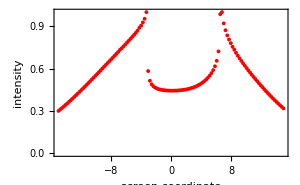

```mathematica
max = Max[Cases[sweep,{x_,y_,i_?NumberQ}/;True:>i]]
Cases[sweep,{x_,y_,i_?NumberQ}/;True:>{x,i/max}];
plot = ListPlot[
	%,
	Joined->False,PlotStyle->{{Thick,Red}},PlotRange->Full, ImageSize->300,
	Frame->True,FrameLabel->{"screen coordinate","intensity"},LabelStyle->{Black,16},FrameStyle->{{Thick,Black}}
]
```

0.00022093574312744537

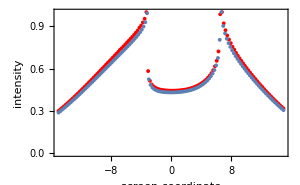

```mathematica
max = Max[Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2][[All,3]]]
Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2:>{x,i/max}];
Show[plot,ListPlot[%]]
```

### code comparison to EXACT_GRRT MODEL-2

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{0,-2,0,1}];
```

#### load comparison data

This loads the image data from TESTCASE 1 and plots it

```mathematica
SetDirectory[NotebookDirectory[]];
intensityEXACT=
Quiet[ToExpression/@Import["EXACT_GRRT_TEST_2_FULL.dat"]];
```

```mathematica
plotDataEXACT = Cases[intensityEXACT[[All,1;;3]],{b_,c_,a_}/;10^2>a>10^-10];
```

```mathematica
Table[{plotDataEXACT[[i,1]],plotDataEXACT[[i,2]],plotDataEXACT[[i,3]]/Max[plotDataEXACT[[All,3]]]},{i,Length@plotDataEXACT}];
ListDensityPlot[plotDataEXACT,ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],
Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
FrameLabel->None(*{"x_screen","y_screen"}*), LabelStyle->{20,Black,Bold},
InterpolationOrder->1, Background->None
]
```

#### compare single image points

```mathematica
rand1 = (*13282*)RandomInteger[{1,Length@intensityEXACT}]
rand2 = RandomInteger[{1,Length@intensityEXACT}]
```

2902

13886

```mathematica
intensityEXACT[[rand1,1;;3]]
intensityEXACT[[rand2,1;;3]]
intensityEXACT[[rand1,3]]/intensityEXACT[[rand2,3]]
```

{5.078740157480315,-9.80314960629921,0.000099923836112035186}

{-0.5905511811023621,10.51181102362205,0.00010534023646953597}

0.9485818473640204

```mathematica
intensity1 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand1, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 60, PrecisionGoal -> 6 ]
intensity2 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand2, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 60, PrecisionGoal -> 6 ]
intensity1/intensity2
```

trajectory escapes: at λ=422.57 the radial coordinate has surpassed the radial camera distance

49.2529

trajectory escapes: at λ=422.38 the radial coordinate has surpassed the radial camera distance

51.0462

0.96487

#### setup intensity sweep

```mathematica
GetScreenSweepWithResolution[pixels_,paramRules_,workingPrecision_] := Module[
	{
		t,xCond,yCond,
		xScreenMin = -15,
		xScreenMax = 15,
		screenPoints,
		iterator=0,
		startTime = AbsoluteTime[],
		intensity = {},
		tRules
	},
	
	screenPoints = RandomSample[Table[{screenXVal,0},{screenXVal,xScreenMin,xScreenMax,(xScreenMax - xScreenMin)/pixels}]];

	intensity = (N@GetIntensityData[{200,π/3,0},paramRules,screenPoints,ode,WorkingPrecision->workingPrecision,PrecisionGoal->4])/.Null->None;
	
	(*SetDirectory[NotebookDirectory[]];
	Export[
		StringJoin[
			"data/sweep",
			"_a_",ToString[Numerator[α/.paramRules]],"$",ToString[Denominator[α/.paramRules]],
			"_lNP_",ToString[Numerator[lNP/.paramRules]],"$",ToString[Denominator[lNP/.paramRules]],
			"_precision_",ToString[Round[workingPrecision]],
			"_resolution_",ToString[Round[pixels]],
			".dat"
		],
		intensity
	];*)
	
	Return[intensity]
];
```

#### get and compare image sweeps

```mathematica
sweep = GetScreenSweepWithResolution[128,{M -> 1, α -> 0},30];
```

84.2139

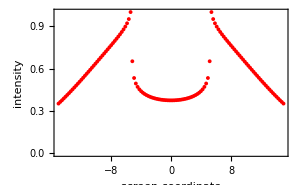

```mathematica
max = Max[Cases[sweep,{x_,y_,i_?NumberQ}/;True:>i]]
Cases[sweep,{x_,y_,i_?NumberQ}/;True:>{x,i/max}];
plot = ListPlot[
	%,
	Joined->False,PlotStyle->{{Thick,Red}},PlotRange->Full, ImageSize->300,
	Frame->True,FrameLabel->{"screen coordinate","intensity"},LabelStyle->{Black,16},FrameStyle->{{Thick,Black}}
]
```

0.00017846523883234518

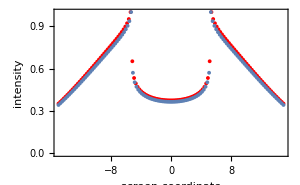

```mathematica
max = Max[Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2][[All,3]]]
Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2:>{x,i/max}];
Show[plot,ListPlot[%]]
```

### code comparison to EXACT_GRRT MODEL-3

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{0,0,10/3,-1}];
```

#### load comparison data

This loads the image data from TESTCASE 3 and plots it

```mathematica
SetDirectory[NotebookDirectory[]];
intensityEXACT=
Quiet[ToExpression/@Import["EXACT_GRRT_TEST_3_FULL.dat"]];
```

```mathematica
plotDataEXACT = Cases[intensityEXACT[[All,1;;3]],{b_,c_,a_}/;10^2>a>10^-10];
```

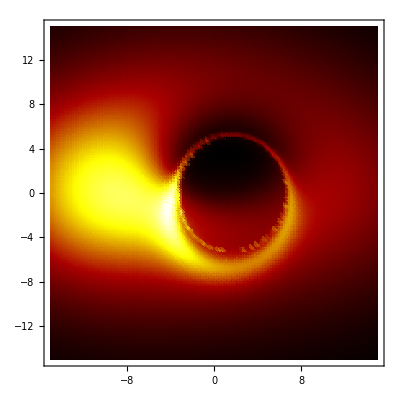

```mathematica
Table[{plotDataEXACT[[i,1]],plotDataEXACT[[i,2]],plotDataEXACT[[i,3]]/Max[plotDataEXACT[[All,3]]]},{i,Length@plotDataEXACT}];
ListDensityPlot[plotDataEXACT,ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],
Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
FrameLabel->None(*{"x_screen","y_screen"}*), LabelStyle->{20,Black,Bold},
InterpolationOrder->1, Background->None
]
```

#### compare single image points

```mathematica
rand1 = (*13282*)RandomInteger[{1,Length@intensityEXACT}]
rand2 = RandomInteger[{1,Length@intensityEXACT}]
```

746

8351

```mathematica
intensityEXACT[[rand1,1;;3]]
intensityEXACT[[rand2,1;;3]]
intensityEXACT[[rand1,3]]/intensityEXACT[[rand2,3]]
```

{9.80314960629921,-13.81889763779528,5.7858341773504679×10^-6}

{-7.913385826771654,0.3543307086614173,0.000076576075191480805}

0.075556682199796915

```mathematica
intensity1 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand1, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity2 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand2, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity1/intensity2
```

trajectory escapes: at λ=421.87 the radial coordinate has surpassed the radial camera distance

2.80708

trajectory escapes: at λ=422.15 the radial coordinate has surpassed the radial camera distance

37.1868

0.075486

#### setup intensity sweep

```mathematica
GetScreenSweepWithResolution[pixels_,paramRules_,workingPrecision_] := Module[
	{
		t,xCond,yCond,
		xScreenMin = -15,
		xScreenMax = 15,
		screenPoints,
		iterator=0,
		startTime = AbsoluteTime[],
		intensity = {},
		tRules
	},
	
	screenPoints = RandomSample[Table[{screenXVal,0},{screenXVal,xScreenMin,xScreenMax,(xScreenMax - xScreenMin)/pixels}]];

	intensity = (N@GetIntensityData[{200,π/3,0},paramRules,screenPoints,ode,WorkingPrecision->workingPrecision,PrecisionGoal->4])/.Null->None;
	
	(*SetDirectory[NotebookDirectory[]];
	Export[
		StringJoin[
			"data/sweep",
			"_a_",ToString[Numerator[α/.paramRules]],"$",ToString[Denominator[α/.paramRules]],
			"_lNP_",ToString[Numerator[lNP/.paramRules]],"$",ToString[Denominator[lNP/.paramRules]],
			"_precision_",ToString[Round[workingPrecision]],
			"_resolution_",ToString[Round[pixels]],
			".dat"
		],
		intensity
	];*)
	
	Return[intensity]
];
```

#### get and compare image sweeps

```mathematica
sweep = GetScreenSweepWithResolution[128,{M -> 1, α -> -9/10},30];
```

43.6134

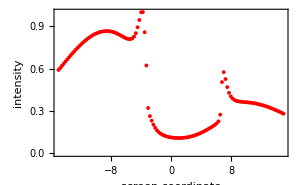

```mathematica
max = Max[Cases[sweep,{x_,y_,i_?NumberQ}/;True:>i]]
Cases[sweep,{x_,y_,i_?NumberQ}/;True:>{x,i/max}];
plot = ListPlot[
	%,
	Joined->False,PlotStyle->{{Thick,Red}},PlotRange->Full, ImageSize->300,
	Frame->True,FrameLabel->{"screen coordinate","intensity"},LabelStyle->{Black,16},FrameStyle->{{Thick,Black}}
]
```

0.000088816153597337459

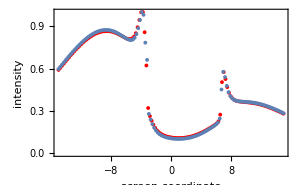

```mathematica
max = Max[Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2][[All,3]]]
Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2:>{x,i/max}];
Show[plot,ListPlot[%]]
```

### code comparison to EXACT_GRRT MODEL-4 (does not work yet)

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{10^5,0,10/3,-1}];
```

#### load comparison data

This loads the image data from TESTCASE 4 and plots it

```mathematica
SetDirectory[NotebookDirectory[]];
intensityEXACT=
Quiet[ToExpression/@Import["EXACT_GRRT_TEST_4_FULL.dat"]];
```

```mathematica
plotDataEXACT = Cases[intensityEXACT[[All,1;;3]],{b_,c_,a_}/;10^2>a>10^-10];
```

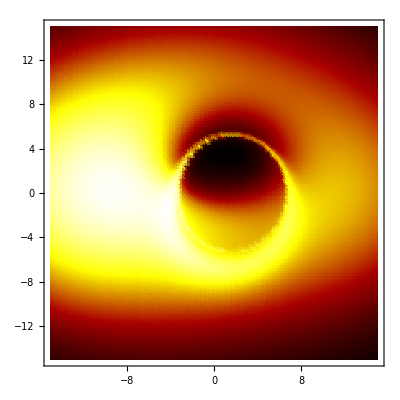

```mathematica
Table[{plotDataEXACT[[i,1]],plotDataEXACT[[i,2]],plotDataEXACT[[i,3]]/Max[plotDataEXACT[[All,3]]]},{i,Length@plotDataEXACT}];
ListDensityPlot[plotDataEXACT,ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],
Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
FrameLabel->None(*{"x_screen","y_screen"}*), LabelStyle->{20,Black,Bold},
InterpolationOrder->1, Background->None
]
```

#### compare single image points

```mathematica
rand1 = (*13282*)RandomInteger[{1,Length@intensityEXACT}]
rand2 = RandomInteger[{1,Length@intensityEXACT}]
```

10977

531

```mathematica
intensityEXACT[[rand1,1;;3]]
intensityEXACT[[rand2,1;;3]]
intensityEXACT[[rand1,3]]/intensityEXACT[[rand2,3]]
```

{7.677165354330708,5.078740157480315,0.000014988207903530211}

{-10.74803149606299,-14.05511811023622,7.073564063039966×10^-6}

2.1189046667216884

```mathematica
intensity1 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand1, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity2 = GetIntensity[{200, π/3, 0},Rationalize[intensityEXACT[[rand2, {1,2}]], 10^-100],{M -> 1, α -> -9/10}, ode,WorkingPrecision -> 40, PrecisionGoal -> 6 ]
intensity1/intensity2
```

trajectory escapes: at λ=423.37 the radial coordinate has surpassed the radial camera distance

9.83201×10^6

trajectory escapes: at λ=421.50 the radial coordinate has surpassed the radial camera distance

9.64952×10^6

1.0189

#### setup intensity sweep

```mathematica
GetScreenSweepWithResolution[pixels_,paramRules_,workingPrecision_] := Module[
	{
		t,xCond,yCond,
		xScreenMin = -15,
		xScreenMax = 15,
		screenPoints,
		iterator=0,
		startTime = AbsoluteTime[],
		intensity = {},
		tRules
	},
	
	screenPoints = RandomSample[Table[{screenXVal,0},{screenXVal,xScreenMin,xScreenMax,(xScreenMax - xScreenMin)/pixels}]];

	intensity = (N@GetIntensityData[{200,π/3,0},paramRules,screenPoints,ode,WorkingPrecision->workingPrecision,PrecisionGoal->4])/.Null->None;
	
	(*SetDirectory[NotebookDirectory[]];
	Export[
		StringJoin[
			"data/sweep",
			"_a_",ToString[Numerator[α/.paramRules]],"$",ToString[Denominator[α/.paramRules]],
			"_lNP_",ToString[Numerator[lNP/.paramRules]],"$",ToString[Denominator[lNP/.paramRules]],
			"_precision_",ToString[Round[workingPrecision]],
			"_resolution_",ToString[Round[pixels]],
			".dat"
		],
		intensity
	];*)
	
	Return[intensity]
];
```

#### get and compare image sweeps

```mathematica
sweep = GetScreenSweepWithResolution[128,{M -> 1, α -> -9/10},30];
```

1.08098×10^7

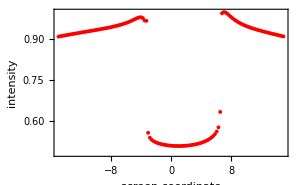

```mathematica
max = Max[Cases[sweep,{x_,y_,i_?NumberQ}/;True:>i]]
Cases[sweep,{x_,y_,i_?NumberQ}/;True:>{x,i/max}];
plot = ListPlot[
	%,
	Joined->False,PlotStyle->{{Thick,Red}},PlotRange->Full, ImageSize->300,
	Frame->True,FrameLabel->{"screen coordinate","intensity"},LabelStyle->{Black,16},FrameStyle->{{Thick,Black}}
]
```

0.000031596163322929428

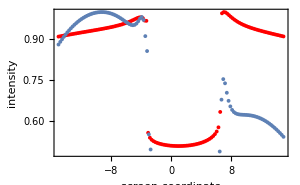

```mathematica
max = Max[Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2][[All,3]]]
Cases[plotDataEXACT,{x_,y_,i_}/;0<y<0.2:>{x,i/max}];
Show[plot,ListPlot[%]]
```

### full image

```mathematica
ode = GetRadiativeTransferEquationForDiskModel[{0,0,10/3,1}];
GetIntensity[{300,π/3,0},{9,9},{M->1,α->-9/10},ode,WorkingPrecision->30,PrecisionGoal->4]
```

trajectory escapes: at λ=632.57 the radial coordinate has surpassed the radial camera distance

16.88

```mathematica
screenBoundary = 10;
pixels = 1000;
screenPoints = Flatten[Table[{screenXVal,screenYVal},{screenXVal,-screenBoundary+1/100,screenBoundary+2/100,(2screenBoundary)/(Sqrt@pixels)},{screenYVal,-screenBoundary+1/100,screenBoundary+2/100,(2screenBoundary)/(Sqrt@pixels)}],1];
intensityList = GetIntensityData[{300,π/3,0},{M->1,α->-9/10},screenPoints,WorkingPrecision->30,PrecisionGoal->4];

RandomSample[intensityList][[1;;2]]//N//TableForm
```

Numerical integration of the radiative transfer equation did not converge for1/1024 screen points. Try to incrase WorkinPrecision and test single points to see error messages.

-1.13562 | 9.61612 | 11.033
-6.82772 | -9.99 | 8.80846

```mathematica
plotData = Cases[intensityList,{x_,y_,i_?NumericQ}];

ListDensityPlot[
	Evaluate[Table[{plotData[[i,1]],plotData[[i,2]],plotData[[i,3]]},{i,Length@plotData}]],
	ColorFunction->Function[Blend[{Black,Darker@Red,Yellow,White},#]],ClippingStyle->{Black,White},
	Frame->True,FrameStyle->Thick, PlotRange->Full,FrameTicks->Automatic,
	FrameLabel->{"x_screen","y_screen"}, LabelStyle->{32,Black},
	InterpolationOrder->0, Background->None, ImageSize->700
]
```

-Graphics-